## Visible Algebra I

### Introduction

This Mathematica notebook is licensed under a  
It creates the demonstrations used in my posts Visible Algebra I and Visible Algebra I supplement.

I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

### Definitions

```mathematica
preop[x_,loc_]:=Text[Framed[Style[x,Medium,FontFamily->"Arial"],Background->White],loc]
```

```mathematica
preop["x",{0,1}]
```

Text[x,{0,1}]

```mathematica
Text["x",{0,1}]
```

Text[x,{0,1}]

```mathematica
DarkGreen:=RGBColor[0,.6,0]
```

```mathematica
Framed[Style[42555,Medium,FontFamily->"Arial"],ImageSize->45,Background->White]
```

42555

```mathematica
fixedop[x_,loc_,width_]:=Text[Framed[Style[x,Medium,FontF;amily->"Arial"],ImageSize->width,Background->White],loc]
```

```mathematica
fixedop[3.13,{0,0},100]
```

Text[3.13,{0,0}]

```mathematica
op[x_,loc_]:=preop[x,loc];op[x_,loc_,width_]:=fixedop[x,loc,width]
```

```mathematica
lab[x_,loc_]:=Text[Style[x,Small,FontFamily->"Arial",Background->White],loc]
```

```mathematica
edge[op1_,op2_,sf_]:=Arrow[{op1,op2},Scaled[sf]]
```

```mathematica
edge[op1_,op2_]:=edge[op1,op2,0]
```

```mathematica
ledge[op1_,op2_,label_]:=Sequence[edge[op1,op2],lab[label,.5(op1+op2)]]
```

```mathematica
fixedop[{Style["Power\n",LineSpacing->{0,1}],PaddedForm[255,4]}//TableForm,{0,0},50]
```

Text[Power

  255,{0,0}]

```mathematica
fixedop[x_,loc_,width_]:=Text[Framed[Style[x,Medium,FontFamily->"Arial"],ImageSize->width,Background->White],loc]
```

```mathematica
calcfop[operation_,formula_,loc_,pad_,width_]:= {Text[Style[operation,Medium,FontFamily->"Arial"]]LineSpacing->{0,1},PaddedForm[formula,pad]}//TableForm,loc,width
```

### The main tree

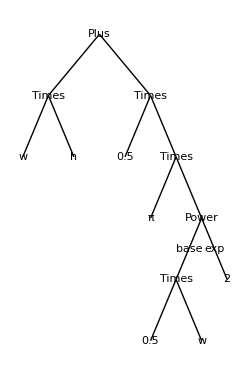

```mathematica
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},{-2,-1}],
edge[{0,0},{2,-1}],
edge[{-2,-1},{-3,-2}],
edge[{-2,-1},{-1,-2}],
edge[{2,-1},{1,-2}],
edge[{2,-1},{3,-2}],
edge[{3,-2},{2,-3}],
edge[{3,-2},{4,-3}],
ledge[{4,-3},{3,-4},"base"],
ledge[{4,-3},{5,-4},"exp"],
edge[{3,-4},{2,-5}],
edge[{3,-4},{4,-5}],
op["Plus",{0,0}],
op["Times",{-2,-1}],
op["Times",{2,-1}],
op[w,{-3,-2}],op[h,{-1,-2}],op[.5,{1,-2}],
op["Times",{3,-2}],
op[Pi,{2,-3}],op["Power",{4,-3}],
op["Times",{3,-4}],op[2,{5,-4}],op[.5,{2,-5}],op[w,{4,-5}],
},
Background->White,ImageSize->250, AspectRatio->1.5
]
]
```

### Evaluation

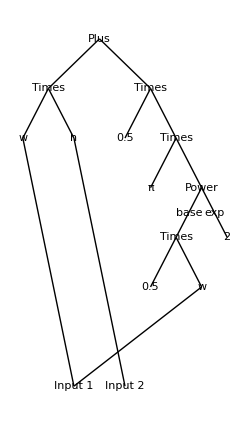

```mathematica
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},{-2,-1}],
edge[{0,0},{2,-1}],
edge[{-2,-1},{-3,-2}],
edge[{-2,-1},{-1,-2}],
edge[{2,-1},{1,-2}],
edge[{2,-1},{3,-2}],
edge[{3,-2},{2,-3}],
edge[{3,-2},{4,-3}],
ledge[{4,-3},{3,-4},"base"],
ledge[{4,-3},{5,-4},"exp"],
edge[{3,-4},{2,-5}],
edge[{3,-4},{4,-5}],
edge[{-1,-7},{-3,-2}],
edge[{-1,-7},{4,-5}],
edge[{1,-7},{-1,-2}],
op["Plus",{0,0}],
op["Times",{-2,-1}],
op["Times",{2,-1}],
op[w,{-3,-2}],op[h,{-1,-2}],op[.5,{1,-2}],
op["Times",{3,-2}],
op[Pi,{2,-3}],op["Power",{4,-3}],
op["Times",{3,-4}],op[2,{5,-4}],op[.5,{2,-5}],op[w,{4,-5}],
op[Style["Input 1",Blue],{-1,-7}],
op[Style["Input 2",DarkGreen],{1,-7}],
},
Background->White,ImageSize->250, AspectRatio->1.7
]
]
```

```mathematica
Manipulate[Show[
Graphics[
{Arrowheads[0],
fixedop[a,{-2+2d/5,0},20],
fixedop[b,{2-2d/5,0},20]
},
ImageSize->150, AspectRatio->.8,PlotRange->{{-4.5,4.5},Automatic}
]
],{{d,1},{1,2,3,4,5,6,7,8}},ControlType->RadioButtonBar,Paneled->False,ControlPlacement->Bottom]
```

```mathematica
Manipulate[x^2,{{x,1},{1,2,3,4,5,6,7},ControlType->RadioButtonBar}]
```

```mathematica
Manipulate[
Show[
Graphics[
{Arrowheads[0],
edge[{0,0},{-2,-1}],
edge[{0,0},{2,-1}],
edge[{-2,-1},{-3,-2}],
edge[{-2,-1},{-1,-2}],
edge[{2,-1},{1,-2}],
edge[{2,-1},{3,-2}],
edge[{3,-2},{2,-3}],
edge[{3,-2},{4,-3}],
ledge[{4,-3},{3,-4},"base"],
ledge[{4,-3},{5,-4},"exp"],
edge[{3,-4},{2,-5}],
edge[{3,-4},{4,-5}],
edge[{-1,-7},{-3,-2}],
edge[{-1,-7},{4,-5}],
edge[{1,-7},{-1,-2}],
op[If[stage≤6,
Style["Plus"],
{Style["Plus\n",LineSpacing->{0,1}],
PaddedForm[Style[h w.5Pi 0.5w^2,Blue],4]
}//TableForm],{0,0},55],
op[If[stage≤5,
Style["Times"],
{Style["Times\n",LineSpacing->{0,1}],
PaddedForm[Style[.5Pi 0.5w^2,Blue],4]
}//TableForm],{2,-1},55],
op[If[stage≤1,
Style["Times"],
{Style["Times\n",LineSpacing->{0,1}],
PaddedForm[Style[h w, Blue],4]
}//TableForm],{-2,-1},55],
op[If[stage==0,Style["w"],Style[w,Blue]],{-3,-2},45],
op[If[stage==0,Style["h"],Style[h,Blue]],{-1,-2},45],op[.5,{1,-2}],
op[If[stage≤3,
Style["Power"],
{Style["Power\n",LineSpacing->{0,1}],
PaddedForm[Style[0.5w^2,Blue],4]
}//TableForm],{4,-3},55],
op[If[stage≤4,
Style["Times"],
{Style["Times\n",LineSpacing->{0,1}],
PaddedForm[Style[Pi 0.5w^2,Blue],4]
}//TableForm],{3,-2},55],
op[Pi,{2,-3}],
op[If[stage≤2,
Style["Times"],
{Style["Times\n",LineSpacing->{0,1}],
PaddedForm[Style[0.5 w,Blue],4]
}//TableForm],{3,-4},55],
op[2,{5,-4}],
op[.5,{2,-5}],
op[If[stage==0,Style["w"],Style[w,Blue]],{4,-5},45],
op[If[stage==0,Style["Input 1"],Style[w,Blue]],{-1,-7},45],
op[If[stage==0,Style["Input 2"],Style[h,Blue]],{1,-7},45]
},
Background->White,ImageSize->250, AspectRatio->1.7
]
],{{stage,0},{0,1,2,3,4,5,6,7}},{{w,1},-.2,4},{{h,1},-.2,4},ControlType->{RadioButtonBar,Slider,Slider},AppearanceElements->{"Horizontal","All","All"},ControlPlacement->Bottom,Paneled->False,SaveDefinitions->True
]
```